```mathematica
Clear["`*"]
```

## Solutions to the Nonlinear equation

## The Spectral Method

Getting the spectrum for
p^(iv) + (c^2-1) p’’-(Q(x)p)’’ -2 c p’_t +p_tt = 0

```mathematica
a0 = 0;
a1 =5;
b2 = 1;
c=1;
```

```mathematica
(*Here is a cool looking picture - assuming I didn't mess anything up - a0 = 0;a1 =5;b1 = 1;
c=1;
This makes for an interesting picture, with curves of spectrum bifurcating off the imaginary axis - Changing a0 from 0 to 1, makes for some more interesting pics - don't have an interesting picture when c = 0 though*)
```

```mathematica
nmodes = 25;
```

```mathematica
d1[μ_]:= DiagonalMatrix[Table[I (k+μ),{k,-nmodes,nmodes}]]
qm = a0 IdentityMatrix[2nmodes+1]+a1*Normal[SparseArray[{Band[{1,2}]->.5,Band[{2,1}]->.5},{2nmodes+1,2nmodes+1}]]+
b2*Normal[SparseArray[{Band[{1,3}]->.5I,Band[{3,1}]->-.5I},{2nmodes+1,2nmodes+1}]];
```

```mathematica
ll[x_]:=ArrayFlatten[{{0,IdentityMatrix[2 nmodes+1]},{d1[x].d1[x].(-d1[x].d1[x]+(qm+(1-c^2)IdentityMatrix[2 nmodes+1])),2c IdentityMatrix[2 nmodes +1].d1[x]}},2]
```

```mathematica
evals1=Flatten[Table[Chop[Eigenvalues[ll[x]]],{x,-1/2,1/2,.005}]];
```

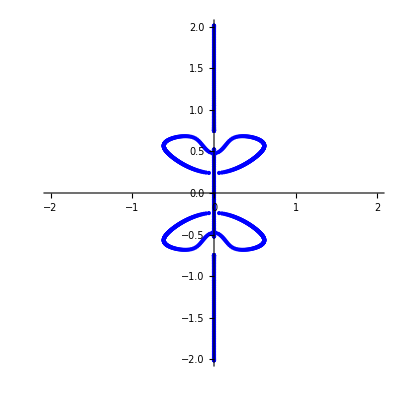

```mathematica
evv=ComplexListPlot[evals1,PlotStyle->{Blue,PointSize[Small]},PlotRange->{{-2,2},{-2,2}},AspectRatio->1]
```

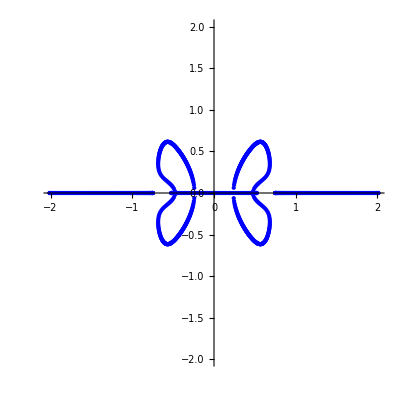

```mathematica
s1=ComplexListPlot[I*evals1,PlotStyle->{Blue,PointSize[Small]},PlotRange->{{-2,2},{-2,2}},AspectRatio->1]
```

## The linear equation

```mathematica
qq[x_]:= a0+a1 Cos[x]+b2 Sin[2x]
per=2Pi;
```

```mathematica
MatrixForm[aa = {{0,0,0,1},{-λ^2,0,0,0},{2 c λ, 1,0,0},{qq[x],0,1,0}}]
```

(0 | 0 | 0 | 1
-λ^2 | 0 | 0 | 0
2 λ | 1 | 0 | 0
5 Cos[x]+Sin[2 x] | 0 | 1 | 0)

```mathematica
MatrixForm[daa = D[aa,λ]]
```

(0 | 0 | 0 | 0
-2 λ | 0 | 0 | 0
2 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
aa.{p[x1],q[x1],r[x1],s[x1]}
aa.{dp[x1],dq[x1],dr[x1],ds[x1]}+daa.{p[x1],q[x1],r[x1],s[x1]}
```

{s[x1],-λ^2 p[x1],2 λ p[x1]+q[x1],r[x1]+p[x1] (5 Cos[x]+Sin[2 x])}

{ds[x1],-λ^2 dp[x1]-2 λ p[x1],2 λ dp[x1]+dq[x1]+2 p[x1],dr[x1]+dp[x1] (5 Cos[x]+Sin[2 x])}

```mathematica
(*sols1[λ_]:=NDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1], dp[x1]==ds[x1], dq[x1]==-λ^2 *dp[x1]-2*λ p[x1],dr[x1]==2 λ dp[x1]+dq[x1]+2 p[x1],ds[x1]==dr[x1]+dp[x1]*qq[x1],p[0]==1,q[0]==0,r[0]==0,s[0]==0,dp[0]==0,dq[0]==0,dr[0]==0,ds[0]==0},{p,q,r,s,dp,dq,dr,ds},{x1,0,20}]*)
```

```mathematica
sols1 =ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],p[0]==1,q[0]==0,r[0]==0,s[0]==0},{p,q,r,s},{x1,0,20},{λ},AccuracyGoal->25];
sols2 =ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],p[0]==0,q[0]==1,r[0]==0,s[0]==0},{p,q,r,s},{x1,0,20},{λ},AccuracyGoal->25];
sols3 =ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],p[0]==0,q[0]==0,r[0]==1,s[0]==0},{p,q,r,s},{x1,0,20},{λ},AccuracyGoal->25];
sols4 =ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],p[0]==0,q[0]==0,r[0]==0,s[0]==1},{p,q,r,s},{x1,0,20},{λ},AccuracyGoal->25];
```

```mathematica
mon[λ_]:= {{sols1[λ][[1]][per],sols2[λ][[1]][per],sols3[λ][[1]][per],sols4[λ][[1]][per]},{sols1[λ][[2]][per],sols2[λ][[2]][per],sols3[λ][[2]][per],sols4[λ][[2]][per]},{sols1[λ][[3]][per],sols2[λ][[3]][per],sols3[λ][[3]][per],sols4[λ][[3]][per]},{sols1[λ][[4]][per],sols2[λ][[4]][per],sols3[λ][[4]][per],sols4[λ][[4]][per]}}
```

```mathematica
tol=10^-2.0;
```

```mathematica
f[λ_]:=Tr[mon[λ]]
g[λ_]:=Chop[(Tr[mon[λ]]^2-Tr[mon[λ].mon[λ]])/2,tol]
fr[λ_]:=Re[Chop[f[λ],tol]]
fim[λ_]:=Im[Chop[f[λ],tol]]
```

```mathematica
del[λ_]:=Discriminant[x^4-(fr[λ]+I*fim[λ])x^3+g[λ] x^2-(fr[λ]-I*fim[λ])x + 1,x ]
```

```mathematica
del[0.2*I]
```

-5.63663×10^13+5.47084×10^-18 ⅈ

```mathematica
del[2*I]
```

-1.27968×10^23-4.70443×10^21 ⅈ

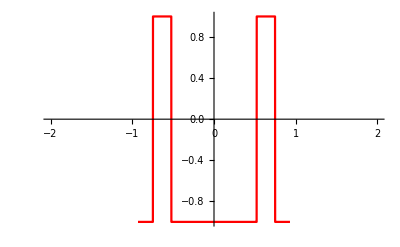

```mathematica
s2=Plot[del[I*k]/Abs[del[I*k]],{k,-2,2},PlotStyle->Red]
```

Looks like this gets the multiplicity correct at least near the origin -though all of the eigenvalues have multiplicity 2 or 0... Not sure why this is so stiff...

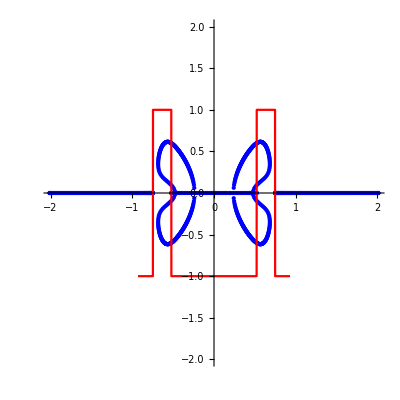

```mathematica
Show[{s1,s2}]
```

```mathematica
Abs[Eigenvalues[mon[0.2*I]]]
```

{236.168,1.,0.999999,0.00424256}

Need to find a potential for c = 0 where the spectrum has some isolas/bifurcations. This might make things easier to compute....

```mathematica
cp= x^4-a[λ]x^3+b[λ]x^2-a[-λ]x+1
dcp =D[cp,λ]
```

1+x^4-x a[-λ]-x^3 a[λ]+x^2 b[λ]

x a'[-λ]-x^3 a'[λ]+x^2 b'[λ]

```mathematica
CharacteristicPolynomial[mon[0.2*I],μ]
```

(1.00195-0.0000398889 ⅈ)-(236.836-24.0043 ⅈ) μ+(454.067+0.000601852 ⅈ) μ^2-(236.833+24.0047 ⅈ) μ^3+μ^4

```mathematica
FullSimplify[Resultant[cp,dcp,x]]
```

a'[-λ]^4+a'[λ]^4-a[-λ] a'[λ]^3 b'[λ]+b[λ] a'[λ]^2 b'[λ]^2-a[λ] a'[λ] b'[λ]^3+b'[λ]^4+a'[-λ]^3 (-((a[λ]^2-2 b[λ]) a'[λ])+a[λ] b'[λ])+a'[-λ]^2 ((2-2 a[-λ] a[λ]+b[λ]^2) a'[λ]^2+(3 a[-λ]-a[λ] b[λ]) a'[λ] b'[λ]+b[λ] b'[λ]^2)+a'[-λ] (-((a[-λ]^2-2 b[λ]) a'[λ]^3)+(-3 a[λ]+a[-λ] b[λ]) a'[λ]^2 b'[λ]+(4-a[-λ] a[λ]) a'[λ] b'[λ]^2+a[-λ] b'[λ]^3)

```mathematica
dsols1=ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],dp'[x1]==ds[x1],dq'[x1]==-λ^2*dp[x1]-2*λ*p[x1],dr'[x1]==2*λ*dp[x1]+dq[x1]+2*p[x1],ds'[x1]==dr[x1]+qq[x1]*dp[x1],
p[0]==1,q[0]==0,r[0]==0,s[0]==0,dp[0]==0,dq[0]==0,dr[0]==0,ds[0]==0},{p,q,r,s,dp,dq,dr,ds},{x1,0,20},{λ},AccuracyGoal->25];
dsols2=ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],dp'[x1]==ds[x1],dq'[x1]==-λ^2*dp[x1]-2*λ*p[x1],dr'[x1]==2*λ*dp[x1]+dq[x1]+2*p[x1],ds'[x1]==dr[x1]+qq[x1]*dp[x1],
p[0]==0,q[0]==1,r[0]==0,s[0]==0,dp[0]==0,dq[0]==0,dr[0]==0,ds[0]==0},{p,q,r,s,dp,dq,dr,ds},{x1,0,20},{λ},AccuracyGoal->25];
dsols3=ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],dp'[x1]==ds[x1],dq'[x1]==-λ^2*dp[x1]-2*λ*p[x1],dr'[x1]==2*λ*dp[x1]+dq[x1]+2*p[x1],ds'[x1]==dr[x1]+qq[x1]*dp[x1],
p[0]==0,q[0]==0,r[0]==1,s[0]==0,dp[0]==0,dq[0]==0,dr[0]==0,ds[0]==0},{p,q,r,s,dp,dq,dr,ds},{x1,0,20},{λ},AccuracyGoal->25];
dsols4=ParametricNDSolveValue[{p'[x1]==s[x1],q'[x1]==-λ^2*p[x1],r'[x1]==2 λ p[x1]+q[x1], s'[x1]==r[x1]+ qq[x1]*p[x1],dp'[x1]==ds[x1],dq'[x1]==-λ^2*dp[x1]-2*λ*p[x1],dr'[x1]==2*λ*dp[x1]+dq[x1]+2*p[x1],ds'[x1]==dr[x1]+qq[x1]*dp[x1],
p[0]==0,q[0]==0,r[0]==0,s[0]==1,dp[0]==0,dq[0]==0,dr[0]==0,ds[0]==0},{p,q,r,s,dp,dq,dr,ds},{x1,0,20},{λ},AccuracyGoal->25];
```

```mathematica
dmon[λ_]:={{dsols1[λ][[5]][per],dsols2[λ][[5]][per],dsols3[λ][[5]][per],dsols4[λ][[5]][per]},{dsols1[λ][[6]][per],dsols2[λ][[6]][per],dsols3[λ][[6]][per],dsols4[λ][[6]][per]},{dsols1[λ][[7]][per],dsols2[λ][[7]][per],dsols3[λ][[7]][per],dsols4[λ][[7]][per]},{dsols1[λ][[8]][per],dsols2[λ][[8]][per],dsols3[λ][[8]][per],dsols4[λ][[8]][per]}}
```

```mathematica
df[λ_]:=Chop[Tr[dmon[λ]],tol]
dg[λ_]:=Tr[mon[λ]]*Tr[dmon[λ]]-Tr[mon[λ].dmon[λ]]
dfr[λ_]:=Re[Chop[df[λ],tol]]
dfim[λ_]:=Im[Chop[df[λ],tol]]
```

```mathematica
df[0.2*I]
```

170.62+17.7621 ⅈ

```mathematica
(f[0.2*I+0.001*I]-f[0.2*I-0.001*I])/((0.2*I+0.001*I)-(0.2*I-0.001*I))
```

170.632+17.7154 ⅈ

```mathematica
FullSimplify[Resultant[cp,dcp,x]]
```

a'[-λ]^4+a'[λ]^4-a[-λ] a'[λ]^3 b'[λ]+b[λ] a'[λ]^2 b'[λ]^2-a[λ] a'[λ] b'[λ]^3+b'[λ]^4+a'[-λ]^3 (-((a[λ]^2-2 b[λ]) a'[λ])+a[λ] b'[λ])+a'[-λ]^2 ((2-2 a[-λ] a[λ]+b[λ]^2) a'[λ]^2+(3 a[-λ]-a[λ] b[λ]) a'[λ] b'[λ]+b[λ] b'[λ]^2)+a'[-λ] (-((a[-λ]^2-2 b[λ]) a'[λ]^3)+(-3 a[λ]+a[-λ] b[λ]) a'[λ]^2 b'[λ]+(4-a[-λ] a[λ]) a'[λ] b'[λ]^2+a[-λ] b'[λ]^3)

```mathematica
bif[λ_]:=df[-λ]^4+df[λ]^4-f[-λ] df[λ]^3 dg[λ]+g[λ] df[λ]^2 dg[λ]^2-f[λ] df[λ] dg[λ]^3+dg[λ]^4+df[-λ]^3 (-((f[λ]^2-2 g[λ]) df[λ])+f[λ] dg[λ])+df[-λ]^2 ((2-2 f[-λ] f[λ]+g[λ]^2) df[λ]^2+(3 f[-λ]-f[λ] g[λ]) df[λ] dg[λ]+g[λ] dg[λ]^2)+df[-λ] (-((f[-λ]^2-2 g[λ]) df[λ]^3)+(-3 f[λ]+f[-λ] g[λ]) df[λ]^2 dg[λ]+(4-f[-λ] f[λ]) df[λ] dg[λ]^2+f[-λ] dg[λ]^3)
```

```mathematica
Bifurcate = ParametricPlot[{Re[bif[I ll]],ll},{ll,-1.2,1.2},PlotStyle->{Red,Dashed}]
PaperFigure=Show[{evv,Bifurcate}]
```

-Graphics-

-Graphics-

```mathematica
Export["~/Dropbox/Jared Robby/Schmoopys/Boussinesq/Figure13.pdf",PaperFigure]
```

~/Dropbox/Jared Robby/Schmoopys/Boussinesq/Figure13.pdf

-Graphics-

-Graphics-